# QMultinomial

QMultinomial[n_1,n_2,…]
q-multinomial coefficient for n_1, n_2, n_3 that approaches ((n_1+n_2+n_3…)!)/(n_1!n_2!n_3!…) as q goes to 1.

## See AlsoSeeAlsoInsert links to any related reference (function) pages.

QBinomial ▪ Binomial ▪ Factorial ▪ QFactorial ▪ QGamma ▪

## Tech NotesTechNotesInsert links to related tech notes.

## Related Guides

## Related LinksRelatedLinksInsert links to any related page, including web pages.

q-Multinomial Coefficient—Wolfram MathWorld

Sagemath's q-analogues support in combinatorics

Gaussian binomial coefficient—Wikipedia

Multinomial—The Wolfram Functions Site

NKS|Online (A New Kind of Science)

Multinomial Coefficient—MathWorld

## Examples InitializationExamplesInitializationInput that is to be evaluated before any examples are run, e.g. Needs[…].

```mathematica
Needs["PeterBurbery`Combinatorics`"]
```

## Basic Examples | More Examples ⊳

Evaluate numerically:

```mathematica
QMultinomial[1,2,1,E]
```

QGamma[5,ⅇ]/(1+ⅇ)

```mathematica
N[QMultinomial[1,2,1,E]]
```

346.47

The 1, 2, 1 multinomial coefficient appears as the coefficient of x y^2 z:

```mathematica
Multinomial[1,2,1]
```

12

```mathematica
Expand[(x+y+z)^4]
```

x^4+4 x^3 y+6 x^2 y^2+4 x y^3+y^4+4 x^3 z+12 x^2 y z+12 x y^2 z+4 y^3 z+6 x^2 z^2+12 x y z^2+6 y^2 z^2+4 x z^3+4 y z^3+z^4

```mathematica
Coefficient[%,x y^2 z]
```

12

Plot over a subset of the reals:

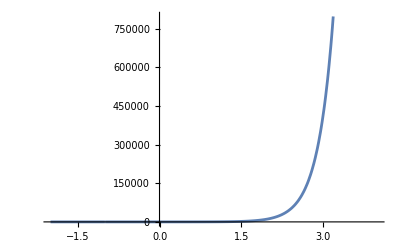

```mathematica
Plot[QMultinomial[x,1/2,3,E],{x,-2,4}]
```

Plot over a subset of the complexes:

```mathematica
ComplexPlot3D[QMultinomial[z,1/2,E],{z,-2-2I,2+2I},PlotLegends->Automatic]
```

-Graphics3D-

Series expansion at the origin:

```mathematica
Series[QMultinomial[x,3,1/2,z],{x,0,2}]//FullSimplify
```

QGamma[9/2,z]/(QGamma[3/2,z] QGamma[4,z])+(QGamma[9/2,z] (-QPolyGamma[0,1,z]+QPolyGamma[0,9/2,z]) x)/(QGamma[3/2,z] QGamma[4,z])+(QGamma[9/2,z] ((QPolyGamma[0,1,z]-QPolyGamma[0,9/2,z])^2-QPolyGamma[1,1,z]+QPolyGamma[1,9/2,z]) x^2)/(2 QGamma[3/2,z] QGamma[4,z])+O[x]^3

Series expansion at Infinitypaclet:ref/Infinity:

```mathematica
Series[QMultinomial[x,2,1/2,E],{x,∞,2}]//FullSimplify
```

QGamma[7/2+x,ⅇ]/((1+ⅇ) QGamma[3/2,ⅇ] QGamma[1+x,ⅇ])

## More ExamplesMoreExamplesExtended examples in standardized sections.

### Scope

### Generalizations & Extensions

### Options

### Applications

### Properties & Relations

### Possible Issues

### Interactive Examples

### Neat Examples

## Metadata

### CategorizationMetadataMetadata such as page URI, context, and type of documentation page.

Symbol

PeterBurbery/Combinatorics

PeterBurbery`Combinatorics`

PeterBurbery/Combinatorics/ref/QMultinomial

### Keywords

### Syntax Templates